```mathematica
bre1=Import["G:\\calc-online\\gpd\\ff\\result\\pionint-xi1.wdx"];
bre2=Import["G:\\calc-online\\gpd\\ff\\result\\pionint-xi2.wdx"];
bre3=Import["G:\\calc-online\\gpd\\ff\\result\\pionint-xi3.wdx"];
```

```mathematica
H1[t_]=Query[1]@bre1+Query[2]@bre1;
H2[t_]=Query[1]@bre2+Query[2]@bre2;
H3[t_]=Query[1]@bre3+Query[2]@bre3;
```

```mathematica
(*calc ac formula*)
```

```mathematica
Solve[H1==a+(2*0.1)^2*c&&H2==a+(2*0.2)^2*c,{a,c}]
```

{{a→1.33333 H1-0.333333 H2,c→-8.33333 H1+8.33333 H2}}

```mathematica
a[t_]=1.3333333333333335 H1[t]-0.33333333333333337 H2[t];
c[t_]=-8.33333333333334 H1[t]+8.333333333333334 H2[t];
```

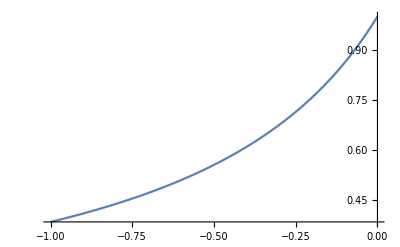

```mathematica
Plot[a[t],{t,-1,0}]
```

```mathematica
H1[-1]
```

0.384215

```mathematica
(*验证ac对ξ无关*)
```

```mathematica
Solve[H1==a+(2*0.1)^2*c&&H3==a+(2*0.3)^2*c,{a,c}]
```

{{a→1.125 H1-0.125 H3,c→-3.125 H1+3.125 H3}}

```mathematica
a2[t_]=1.1250000000000002 H1[t]-0.12500000000000006 H3[t];
c2[t_]=-3.1250000000000036 H1[t]+3.125000000000001 H3[t];
```

```mathematica
Plot[a2[t],{t,-1,0}]
```

-Graphics-

```mathematica
a[t]-a2[t]
```

-0.333333 (0.+0.999846/(1-1.60231 t))+0.208333 (0.+0.999846/(1-1.60231 t))+0.125 (0.+0.999846/(1-1.60231 t))

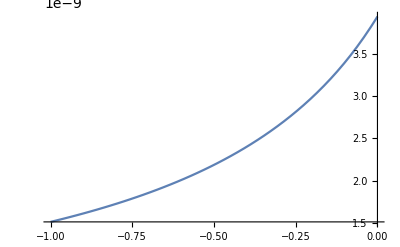

```mathematica
Plot[a[t]-a2[t],{t,-1,0}]
```

```mathematica
ACoutput=<|"A"->a[t],"C"->c[t]|>;
path=FileNameJoin[{"G:\\calc-online\\gpd\\ff\\result",
"pionac.wdx"}];
```

```mathematica
Export[path,ACoutput]
```

G:\calc-online\gpd\ff\result\pionac.wdx